# Cosmomathica v1.0

Santiago Casas, 2018

This notebook demonstrates how to use the Cosmomathica package version 1.0

## Calling external programs

### Initialization

First, load the Cosmomathica package

```mathematica
Directory[]
```

/local/home/scasas

```mathematica
SetDirectory[NotebookDirectory[]]
```

/local/home/scasas/CosmoProjects/cosmomathica

```mathematica
<<(NotebookDirectory[]<>"cosmomathica.m")
```

### CAMB

CAMB takes a lot of parameters. In Cosmomathica, most of them are being treated as options with default values while some of them are regular parameters that have to be specified. The distinction is arbitrary. These are the default options (see the CAMB documentation for details):

```mathematica
?CAMB
```

CAMB[OmegaC, OmegaB, h] :
provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.

```mathematica
Options[CAMB]
```

{MGflag→0,pureMGflag→1,altMGflag→1,QSAflag→1,mugammapar→2,musigmapar→1,QRpar→1,DEmodel→1,GRtrans→0.001,B1→0.,lambda12→0.,B2→0.,lambda22→0.,ss→4.,E11→0.,E22→0.,mu0→-1.,sigma0→0.,MGQfix→0.,MGRfix→0.,Qnot→1.,Rnot→1.,sss→0.,Lindergamma→0.545,betastar→0.,astar→0.5,xistar→0.001,beta0→1.,xi0→0.0001,DilS→0.24,DilR→1.,FR0→0.0001,FRn→1.,w0ppf→-1.,wappf→0.,Tcmb→2.7255,OmegaNu→0,OmegaK0→0.,YHe→0.24,MasslessNeutrinos→3.046,MassiveNeutrinos→0,NuMassDegeneracies→{0},NuMassFractions→{1},ScalarInitialCondition→adiabatic,NonLinear→pk,HalofitVersion→4,WantCMB→True,WantTransfer→True,WantCls→False,WantScalars→False,WantVectors→False,WantTensors→False,ScalarSpectralIndex→{0.96},ScalarRunning→{0},TensorSpectralIndex→{0},RatioScalarTensorAmplitudes→{1},ScalarPowerAmplitude→{2.1×10^-9},PivotScalar→0.05,PivotTensor→0.05,DoReionization→True,UseOpticalDepth→False,OpticalDepth→0.,ReionizationRedshift→10.,ReionizationFraction→1.,ReionizationDeltaRedshift→0.5,AccuracyBoost→2,TransferHighPrecision→True,TransferInterpMatterPower→False,WantZstar→True,WantZdrag→True,OutputNormalization→1,MaxEll→1500,MaxEtaK→4000.,MaxEtaKTensor→800.,MaxEllTensor→400,TransferKmax→5,TransferKperLogInt→50,TransferRedshifts→{0.},AccuratePolarization→True,AccurateReionization→False,AccurateBB→False,DoLensing→False,OnlyTransfers→False,DerivedParameters→True,MassiveNuMethod→best,debugIntFloats→False}

```mathematica
?MGflag
```

An option for CAMB/MGCAMB: 
          MG_flag = 0 :  default GR
          MG_flag = 1 :  pure MG models
          MG_flag = 2 :  alternative MG models
          MG_flag = 3 :  QSA models

```mathematica
?QSAflag
```

An option for CAMB/MGCAMB: 
QSA_flag = 1 : f(R)
QSA_flag = 2 : Symmetron      
QSA_flag = 3 : Dilaton
QSA_flag = 4 : Hu-Sawicki f(R)

```mathematica
?FR0
```

Parameter options for MGCAMB

```mathematica
?MasslessNeutrinos
```

An option for CAMB

```mathematica
?HalofitVersion
```

An option for CAMB. Integer number that chooses the Halofit version used in the non-linear matter power spectrum.
1: Original, 2: Bird, 3: Peacock, 4: Takahashi, 5: Mead, 6: Halo model, 7: Casarini,
8: Mead2015, 9: Winther-f(R)

Default values of some CAMB default options:

```mathematica
OptionValue[CAMB,#]&/@{MGflag,FR0,FRn, OmegaNu,MasslessNeutrinos,NuMassDegeneracies,NuMassFractions,ScalarSpectralIndex,ScalarPowerAmplitude,MaxEtaK,TransferKmax, HalofitVersion}
```

{0,0.0001,1.,0,3.046,{0},{1},{0.96},{2.1×10^-9},4000.,5,4}

Run the CAMB code (without lensing the scalar angular power spectrum will contain only three curves corresponding to C_TT, C_EE, C_TE - see the CAMB documentation for further information) with the transfer function for two different redshifts

```mathematica
Interrupt[]
```

$Aborted

```mathematica
redshifts=Reverse[Range[0,3,0.5]]
```

{3.,2.5,2.,1.5,1.,0.5,0.}

```mathematica
ClearAll[cambdata]
```

```mathematica
cambdata[0]=CAMB[0.25,0.05,0.67,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->4, MGflag->0]
```

{CAMB[age]→14.0639,17,CAMB[Transfer]→{{{5.14524×10^-6,6.61383×10^6,6.61383×10^6,8.81811×10^6,8.8181×10^6,0.,6.61383×10^6,6.61383×10^6,6.62478×10^6,-0.596389,6.48321×10^6,6.48321×10^6,5.4013},{5.6823×10^-6,6.61382×10^6,6.61382×10^6,8.81803×10^6,8.81802×10^6,0.,6.61382×10^6,6.61382×10^6,6.62478×10^6,-0.596389,6.48321×10^6,6.48321×10^6,5.96506},360,{5.06605,1792.24,1764.75,0.0000199572,0.0000179722,0.,1787.66,1787.66,1787.66,-0.000160718,1751.79,1750.55,0.0000909674}},5,{{1},361,{1}}}}
 |  |  |  |

```mathematica
cambdata[1]=CAMB[0.25,0.05,0.67,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->4, MGflag->3, QSAflag->4, FR0->10^(-10), FRn->1, DEmodel->0]
```

{CAMB[age]→14.0639,17,CAMB[Transfer]→{{{5.14524×10^-6,6.61383×10^6,6.61383×10^6,8.81811×10^6,8.8181×10^6,0.,6.61383×10^6,6.61383×10^6,6.62478×10^6,-0.596389,6.48321×10^6,6.48321×10^6,5.4013},{5.6823×10^-6,6.61382×10^6,6.61382×10^6,8.81803×10^6,8.81802×10^6,0.,6.61382×10^6,6.61382×10^6,6.62478×10^6,-0.596389,6.48321×10^6,6.48321×10^6,5.96506},360,{5.06605,1792.51,1765.02,0.0000199459,0.000018603,0.,1787.93,1787.93,1787.93,-0.000160743,1751.71,1750.47,0.0000909756}},5,{1}}}
 |  |  |  |

```mathematica
cambdata[2]=CAMB[0.25,0.05,0.67,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->4, MGflag->3, QSAflag->4, FR0->10^(-4), FRn->1, DEmodel->0, GRtrans->1.0]
```

{CAMB[age]→14.0639,17,CAMB[Transfer]→{{{5.14524×10^-6,6.61383×10^6,6.61383×10^6,8.81811×10^6,8.8181×10^6,0.,6.61383×10^6,6.61383×10^6,6.62478×10^6,-0.596389,6.48321×10^6,6.48321×10^6,5.4013},{5.6823×10^-6,6.61382×10^6,6.61382×10^6,8.81803×10^6,8.81802×10^6,0.,6.61382×10^6,6.61382×10^6,6.62478×10^6,-0.596389,6.48321×10^6,6.48321×10^6,5.96506},360,{5.06605,1792.24,1764.75,0.0000199572,0.0000179722,0.,1787.66,1787.66,1787.66,-0.000160718,1751.79,1750.55,0.0000909674}},5,{{1},361,{1}}}}
 |  |  |  |

```mathematica
SetDirectory[NotebookDirectory[]]
```

/local/home/scasas/CosmoProjects/cosmomathica

```mathematica
Options[CAMB]
```

{MGflag→0,pureMGflag→1,altMGflag→1,QSAflag→1,mugammapar→2,musigmapar→1,QRpar→1,DEmodel→1,GRtrans→0.001,B1→0.,lambda12→0.,B2→0.,lambda22→0.,ss→4.,E11→0.,E22→0.,mu0→-1.,sigma0→0.,MGQfix→0.,MGRfix→0.,Qnot→1.,Rnot→1.,sss→0.,Lindergamma→0.545,betastar→0.,astar→0.5,xistar→0.001,beta0→1.,xi0→0.0001,DilS→0.24,DilR→1.,FR0→0.0001,FRn→1.,w0ppf→-1.,wappf→0.,Tcmb→2.7255,OmegaNu→0,OmegaK0→0.,YHe→0.24,MasslessNeutrinos→3.046,MassiveNeutrinos→0,NuMassDegeneracies→{0},NuMassFractions→{1},ScalarInitialCondition→adiabatic,NonLinear→pk,HalofitVersion→4,WantCMB→True,WantTransfer→True,WantCls→False,WantScalars→False,WantVectors→False,WantTensors→False,ScalarSpectralIndex→{0.96},ScalarRunning→{0},TensorSpectralIndex→{0},RatioScalarTensorAmplitudes→{1},ScalarPowerAmplitude→{2.1×10^-9},PivotScalar→0.05,PivotTensor→0.05,DoReionization→True,UseOpticalDepth→False,OpticalDepth→0.,ReionizationRedshift→10.,ReionizationFraction→1.,ReionizationDeltaRedshift→0.5,AccuracyBoost→2,TransferHighPrecision→True,TransferInterpMatterPower→False,WantZstar→True,WantZdrag→True,OutputNormalization→1,MaxEll→1500,MaxEtaK→4000.,MaxEtaKTensor→800.,MaxEllTensor→400,TransferKmax→5,TransferKperLogInt→50,TransferRedshifts→{0.},AccuratePolarization→True,AccurateReionization→False,AccurateBB→False,DoLensing→False,OnlyTransfers→False,DerivedParameters→True,MassiveNuMethod→best,debugIntFloats→False}

```mathematica
cambdata[0][[All,1]]
```

{CAMB[age],CAMB[zstar],CAMB[rstar],CAMB[100thetastar],CAMB[zdrag],CAMB[rdrag],CAMB[kD],CAMB[100thetaD],CAMB[zEQ],CAMB[100thetaEQ],CAMB[H(z)],CAMB[sigma8(z)],CAMB[f(z)],CAMB[D+(z)],CAMB[CLscalar],CAMB[redshifts],CAMB[PSlinear],CAMB[PSnonlinear],CAMB[Transfer]}

```mathematica
Reverse[redshifts]
```

{0.,0.5,1.,1.5,2.,2.5,3.}

```mathematica
redshiftsz[0]=CAMB["redshifts"]/.cambdata[0]
```

{3.,2.5,2.,1.5,1.,0.5,0.}

```mathematica
ClearAll[hofz]
```

```mathematica
hofz[0]=CAMB["H(z)"]/.cambdata[0]
```

{0.000997564,0.00082347,0.000663257,0.000518913,0.000393586,0.000292502,0.000223498}

```mathematica
Transpose[Reverse[#]&/@{redshiftsz[0], growth[0], growthrate[0],sigma8[0]}]
```

{{0.,1.,0.512757,0.785823},{0.5,0.773212,0.749082,0.607607},{1.,0.61187,0.869019,0.480821},{1.5,0.500542,0.926371,0.393337},{2.,0.421564,0.955243,0.331274},{2.5,0.363377,0.970876,0.28555},{3.,0.318993,0.979932,0.250672}}

```mathematica
cambdata[-1]=Import["./stdCAMB-linPk-z0.txt", "Table"];
```

```mathematica
cambdata[-2]=Import["./stdCAMB-nonlinPk-z0.txt", "Table"];
```

```mathematica
Do[
Print["ii:", ii];
cambdata[ii]=CAMB[0.25,0.05,0.67,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->9, MGflag->3, QSAflag->4, FR0->10^(-ii), FRn->1, DEmodel->0];
,{ii,{4,5,6}}]
```

ii:4

ii:5

ii:6

```mathematica
Do[
Do[
Print["ii:", ii, "  , z:", redz];
kvals[ii][redz]=((CAMB["PSlinear"]/.cambdata[ii])[[redz]])[[All,1]];
psl[ii][redz]=((CAMB["PSlinear"]/.cambdata[ii])[[redz]])[[All,2]];
psnl[ii][redz]=((CAMB["PSnonlinear"]/.cambdata[ii])[[redz]])[[All,2]];
tr[ii][redz]=((CAMB["Transfer"]/.cambdata[ii])[[redz]])[[All,2]];
growth[ii]=(CAMB["D+(z)"]/.cambdata[ii]);
growthrate[ii]=(CAMB["f(z)"]/.cambdata[ii]);
hofz[ii]=(CAMB["H(z)"]/.cambdata[ii]);
ratioLin[ii][redz]=psl[ii][redz]/psl[0][redz];
ratioNonLin[ii][redz]=psnl[ii][redz]/psnl[0][redz];
(*Export["./powerspectra/cosmomathica-fR-"<>ToString[ii]<>"-pk_lin-z_"<>ToString[Length[redshifts]-redz]<>".txt", Transpose[{kvals[ii][redz],psl[ii][redz]}], "Table"];*)
(*Export["./powerspectra/cosmomathica-fR-"<>ToString[ii]<>"-pk_nonlin-z_"<>ToString[Length[redshifts]-redz]<>".txt", Transpose[{kvals[ii][redz],psnl[ii][redz]}], "Table"];*)
,{ii,{0,4,5,6}}];
,
{redz, Range[Length[redshifts]]}]
```

ii:0  , z:1

ii:4  , z:1

ii:5  , z:1

ii:6  , z:1

ii:0  , z:2

ii:4  , z:2

ii:5  , z:2

ii:6  , z:2

ii:0  , z:3

ii:4  , z:3

ii:5  , z:3

ii:6  , z:3

ii:0  , z:4

ii:4  , z:4

ii:5  , z:4

ii:6  , z:4

ii:0  , z:5

ii:4  , z:5

ii:5  , z:5

ii:6  , z:5

ii:0  , z:6

ii:4  , z:6

ii:5  , z:6

ii:6  , z:6

ii:0  , z:7

ii:4  , z:7

ii:5  , z:7

ii:6  , z:7

Age of the universe:

```mathematica
CAMB["age"]/.cambdata[0]
```

14.0639

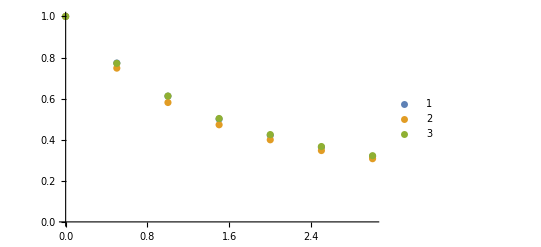

```mathematica
ListPlot[{Transpose[{redshifts,growth[0]}], Transpose[{redshifts,growth[4]}], Transpose[{redshifts,growth[6]}]}, PlotLegends->Automatic]
```

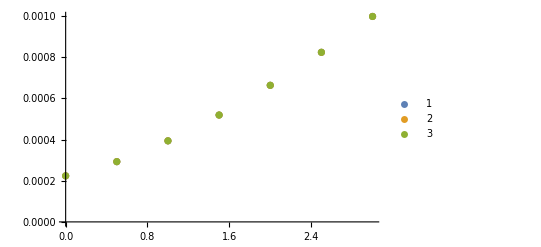

```mathematica
ListPlot[{Transpose[{redshifts,hofz[0]}], Transpose[{redshifts,hofz[4]}], Transpose[{redshifts,hofz[6]}]}, PlotLegends->Automatic]
```

There is a σ_8 for each redshift and for each spectral index

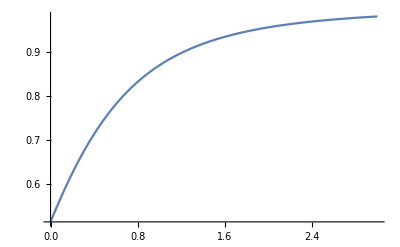

```mathematica
Plot[fg[zz ], {zz,0.,3.0}]
```

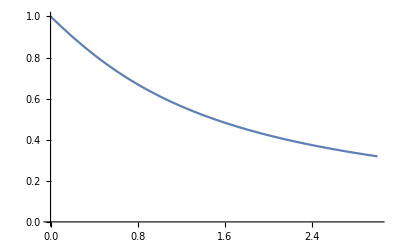

```mathematica
ListPlot[{Thread[{redshifts,growth[0]}]}, Joined->True]
```

Plot the scalar angular power spectrum for TT

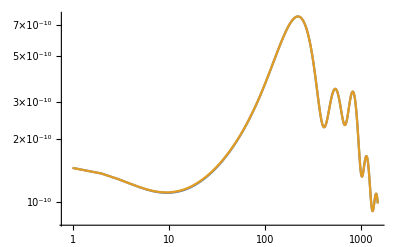

```mathematica
ListLogLogPlot[{(CAMB["CLscalar"]/.cambdata[0])[[1]],(CAMB["CLscalar"]/.cambdata[4])[[1]]} ,Joined->True]
```

Plot the scalar angular power spectrum for EE and TE

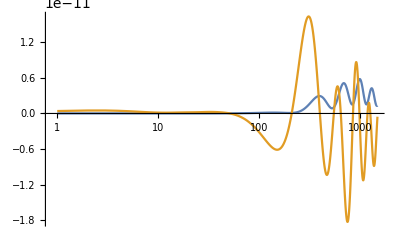

```mathematica
ListLogLinearPlot[(CAMB["CLscalar"]/.cambdata[0])[[2;;3]],Joined->True]
```

The results for the linear/nonlinear power spectrum as well as the transfer function contain a list for each redshift. Each one of those is a list of number pairs {k_i,P(k_i)} in the case of the power spectrum, and a list of seven numbers {k_i,T_1(k_i),..., T_6(k_i)} in case of the transfer function, each of which correspond to CDM, baryon, photon, massless neutrino, massive neutrinos, and total (massive).

Plot the nonlinear matter power spectrum for all redshifts

```mathematica
CAMB["redshifts"]/.cambdata[0]
```

{2.,1.,0.}

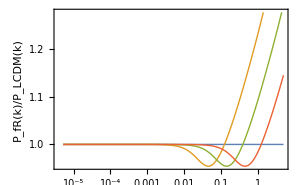

```mathematica
raplo=ListLogLinearPlot[Evaluate@((Thread[{kvals[#],ratioLin[#]}]&/@{0,4,5,6})),Joined->True (*PlotLegends->Placed[LineLegend[{"logfR0=-4,","logfR0=-5", "logfR0=-6", "LCDM"}], Scaled[{0.1,0.8}]]*), PlotStyle->Thick, Frame->True, FrameLabel->{"", Style["P_fR(k)/P_LCDM(k)", Bold, 10]} , ImageSize->{300,150}, FrameTicksStyle->Directive[Black,10]]
```

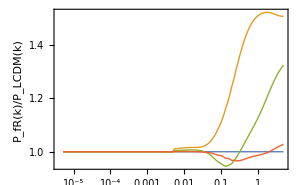

```mathematica
raplonl=ListLogLinearPlot[Evaluate@((Thread[{kvals[#],ratioNonLin[#]}]&/@{0,4,5,6})),Joined->True (*PlotLegends->Placed[LineLegend[{"logfR0=-4,","logfR0=-5", "logfR0=-6", "LCDM"}], Scaled[{0.1,0.8}]]*), PlotStyle->Thick, Frame->True, FrameLabel->{"", Style["P_fR(k)/P_LCDM(k)", Bold, 10]} , ImageSize->{300,150}, FrameTicksStyle->Directive[Black,10]]
```

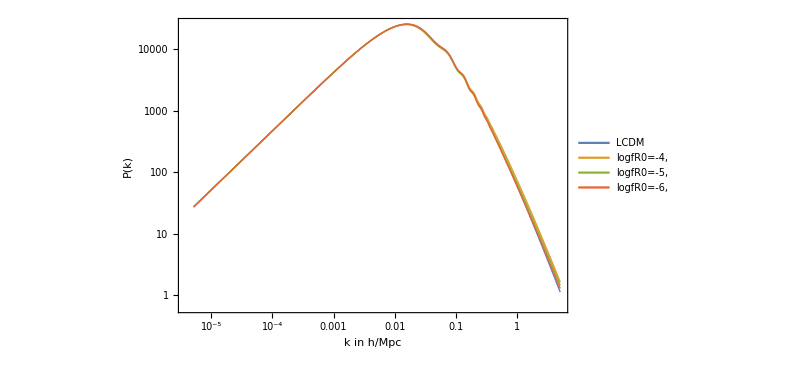

```mathematica
ListLogLogPlot[Evaluate@((Thread[{kvals[#],psl[#]}]&/@{0,4,5,6}))~Join~{},Joined->True, PlotLegends->Placed[LineLegend[{"LCDM","logfR0=-4,","logfR0=-5,","logfR0=-6,"}], Scaled[{0.2,0.8}]], PlotStyle->Thick, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16], Epilog->Inset[raplo, Scaled[{0.5,0.3}]]]
```

```mathematica
colorarra=ColorData["DarkRainbow"][#]&/@Subdivide[1,3]
```

{RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335],RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333],RGBColor[0.72987, 0.239399, 0.230961]}

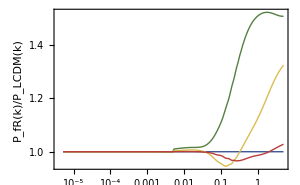

```mathematica
raplonl=ListLogLinearPlot[Evaluate@((Thread[{kvals[#],ratioNonLin[#]}]&/@{0,4,5,6})),Joined->True (*PlotLegends->Placed[LineLegend[{"logfR0=-4,","logfR0=-5", "logfR0=-6", "LCDM"}], Scaled[{0.1,0.8}]]*), PlotStyle->Thread[{ConstantArray[Thick,Length@colorarra],colorarra}], Frame->True, FrameLabel->{"", Style["P_fR(k)/P_LCDM(k)", Bold, 10]} , ImageSize->{300,150}, FrameTicksStyle->Directive[Black,10]]
```

```mathematica
Thread[{ConstantArray[Thick,2*Length@colorarra],colorarra~Join~colorarra}]
```

{{Thickness[Large],RGBColor[0.237736, 0.340215, 0.575113]},{Thickness[Large],RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335]},{Thickness[Large],RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333]},{Thickness[Large],RGBColor[0.72987, 0.239399, 0.230961]},{Thickness[Large],RGBColor[0.237736, 0.340215, 0.575113]},{Thickness[Large],RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335]},{Thickness[Large],RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333]},{Thickness[Large],RGBColor[0.72987, 0.239399, 0.230961]}}

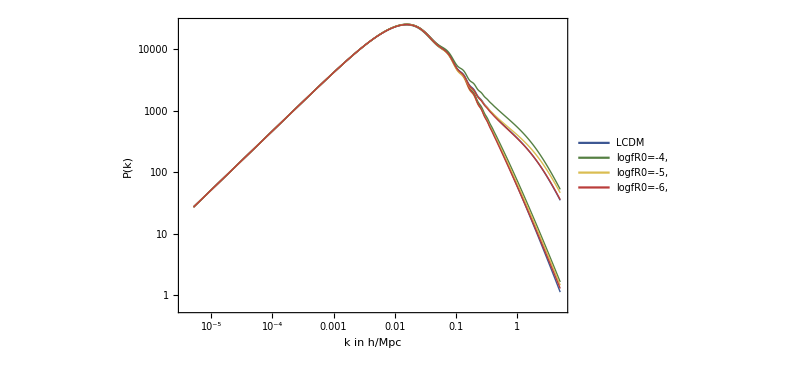

```mathematica
ListLogLogPlot[Evaluate@((Thread[{kvals[#],psl[#]}]&/@{0,4,5,6}))~Join~Evaluate@((Thread[{kvals[#],psnl[#]}]&/@{0,4,5,6})),Joined->True, PlotLegends->Placed[LineLegend[{"LCDM","logfR0=-4,","logfR0=-5,","logfR0=-6,"}], Scaled[{0.2,0.8}]], PlotStyle->Thread[{ConstantArray[Thick,2*Length@colorarra],colorarra~Join~colorarra}], Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl, Scaled[{0.5,0.3}]]]
```

```mathematica
ConstantArray[Thick,8]
```

{Thickness[Large],Thickness[Large],Thickness[Large],Thickness[Large],Thickness[Large],Thickness[Large],Thickness[Large],Thickness[Large]}

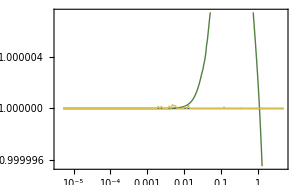

```mathematica
raplonl=ListLogLinearPlot[Evaluate@((Thread[{kvals[#],ratioNonLin[#]}]&/@{0,1,2})),Joined->True (*PlotLegends->Placed[LineLegend[{"logfR0=-4,","logfR0=-5", "logfR0=-6", "LCDM"}], Scaled[{0.1,0.8}]]*), PlotStyle->Thread[{ConstantArray[Thick,Length@colorarra],colorarra}], Frame->True, FrameLabel->{"", Style["P_fR(k)/P_LCDM(k)", Bold, 10]} , ImageSize->{300,150}, FrameTicksStyle->Directive[Black,10]]
```

```mathematica
colorarra=Reverse[ColorData["DarkRainbow"][#]&/@Subdivide[1,3]]
```

{RGBColor[0.72987, 0.239399, 0.230961],RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333],RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335],RGBColor[0.237736, 0.340215, 0.575113]}

```mathematica
cambdata[-2];
```

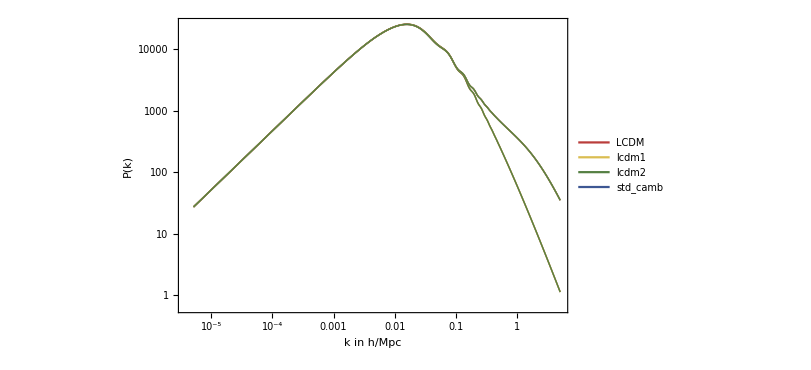

```mathematica
ListLogLogPlot[Evaluate@((Thread[{kvals[#],psl[#]}]&/@{0,1,2}))~Join~Evaluate@((Thread[{kvals[#],psnl[#]}]&/@{0,1,2}))~Join~{cambdata[-2]},Joined->True, PlotLegends->Placed[LineLegend[{"LCDM","lcdm1","lcdm2", "std_camb"}], Scaled[{0.2,0.8}]], PlotStyle->Thread[{ConstantArray[Thick,2*Length@colorarra],colorarra~Join~colorarra}], Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16], Epilog->Inset[raplonl, Scaled[{0.5,0.3}]]]
```